```mathematica
Needs["Notation`"];
Notation[Δ ⟺ cd]
Notation[𝒿 ⟺ cj]
```

```mathematica
<<sneg`sneg`;
snegfermionoperators[a,b,c];
snegrealconstants[cj,U,U1,t,t22,t23,cd,x];
```

sneg 1.250 Copyright (C) 2016 Rok Zitko

```mathematica
myop = {a[1],a[2],a[3],a[4],a[5],a[6]}
```

{a^,a[2],a[3],a[4],a[5],a[6]}

```mathematica
makebasis[myop]
```

{a_(1⇑)^†,a_(1↓)^†,a_(2⇑)^†,a_(2↓)^†,a_(3⇑)^†,a_(3↓)^†,a_(4⇑)^†,a_(4↓)^†,a_(5⇑)^†,a_(5↓)^†,a_(6⇑)^†,a_(6↓)^†}

```mathematica
vc6= qszbasisvc[myop];
```

```mathematica
basise4p2 = Select[vc6,#[[1]]=={-2,2}&][[1,2]];
```

```mathematica
basise4p1 = Select[vc6,#[[1]]=={-2,1}&][[1,2]];
```

```mathematica
basise40 = Select[vc6,#[[1]]=={-2,0}&][[1,2]];
```

```mathematica
basise4n1 = Select[vc6,#[[1]]=={-2,-1}&][[1,2]];
```

```mathematica
basise4n2= Select[vc6,#[[1]]=={-2,-2}&][[1,2]];
```

```mathematica
hhop = -t22(hop[a[2],a[5]])- t22(hop[a[3],a[6]])-t23(hop[a[2],a[6]]+hop[a[3],a[5]])
```

-t22 (a_(2↓)^†·a_(5↓)^+a_(2⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(2↓)^+a_(5⇑)^†·a_(2⇑)^)-t23 (a_(2↓)^†·a_(6↓)^+a_(2⇑)^†·a_(6⇑)^+a_(3↓)^†·a_(5↓)^+a_(3⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(3↓)^+a_(5⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(2↓)^+a_(6⇑)^†·a_(2⇑)^)-t22 (a_(3↓)^†·a_(6↓)^+a_(3⇑)^†·a_(6⇑)^+a_(6↓)^†·a_(3↓)^+a_(6⇑)^†·a_(3⇑)^)

```mathematica
hhd = cd(number[a[3]]+number[a[6]])(* 0.0(number[a[1]]+number[a[2]]+number[a[4]]+number[a[5]])*)
```

Δ (a_(3↓)^†·a_(3↓)^+a_(3⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(6↓)^+a_(6⇑)^†·a_(6⇑)^)

```mathematica
hhj = (U-3cj)(nc[number[a[1],UP],number[a[2],UP]]+nc[number[a[1],UP],number[a[3],UP]]+nc[number[a[2],UP],number[a[3],UP]]+nc[number[a[1],DO],number[a[2],DO]]+nc[number[a[1],DO],number[a[3],DO]]+nc[number[a[2],DO],number[a[3],DO]]+nc[number[a[4],UP],number[a[5],UP]]+nc[number[a[4],UP],number[a[6],UP]]+nc[number[a[5],UP],number[a[6],UP]]+nc[number[a[4],DO],number[a[5],DO]]+nc[number[a[4],DO],number[a[6],DO]]+nc[number[a[5],DO],number[a[6],DO]])
```

(-3 𝒿+U) (-(a_(1↓)^†·a_(2↓)^†·a_(1↓)^·a_(2↓)^)-a_(1↓)^†·a_(3↓)^†·a_(1↓)^·a_(3↓)^-a_(1⇑)^†·a_(2⇑)^†·a_(1⇑)^·a_(2⇑)^-a_(1⇑)^†·a_(3⇑)^†·a_(1⇑)^·a_(3⇑)^-a_(2↓)^†·a_(3↓)^†·a_(2↓)^·a_(3↓)^-a_(2⇑)^†·a_(3⇑)^†·a_(2⇑)^·a_(3⇑)^-a_(4↓)^†·a_(5↓)^†·a_(4↓)^·a_(5↓)^-a_(4↓)^†·a_(6↓)^†·a_(4↓)^·a_(6↓)^-a_(4⇑)^†·a_(5⇑)^†·a_(4⇑)^·a_(5⇑)^-a_(4⇑)^†·a_(6⇑)^†·a_(4⇑)^·a_(6⇑)^-a_(5↓)^†·a_(6↓)^†·a_(5↓)^·a_(6↓)^-a_(5⇑)^†·a_(6⇑)^†·a_(5⇑)^·a_(6⇑)^)

```mathematica
hhu = U(hubbard[a[1]]+hubbard[a[2]]+hubbard[a[3]]+hubbard[a[4]]+hubbard[a[5]]+hubbard[a[6]])
```

U (-(a_(1↓)^†·a_(1⇑)^†·a_(1↓)^·a_(1⇑)^)-a_(2↓)^†·a_(2⇑)^†·a_(2↓)^·a_(2⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(3↓)^·a_(3⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(4↓)^·a_(4⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(5↓)^·a_(5⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(6↓)^·a_(6⇑)^)

```mathematica
hhu1 = (*U1(nc[number[a[1],UP],number[a[2],UP]]+nc[number[a[1],UP],number[a[3],UP]]+nc[number[a[2],UP],number[a[3],UP]]+nc[number[a[1],DO],number[a[2],DO]]+nc[number[a[1],DO],number[a[3],DO]]+nc[number[a[2],DO],number[a[3],DO]]+nc[number[a[4],UP],number[a[5],UP]]+nc[number[a[4],UP],number[a[6],UP]]+nc[number[a[5],UP],number[a[6],UP]]+nc[number[a[4],DO],number[a[5],DO]]+nc[number[a[4],DO],number[a[6],DO]]+nc[number[a[5],DO],number[a[6],DO]])+*)(U-2cj)(nc[number[a[1],UP],number[a[2],DO]]+nc[number[a[1],UP],number[a[3],DO]]+nc[number[a[2],UP],number[a[3],DO]]+nc[number[a[1],DO],number[a[2],UP]]+nc[number[a[1],DO],number[a[3],UP]]+nc[number[a[2],DO],number[a[3],UP]]+nc[number[a[4],UP],number[a[5],DO]]+nc[number[a[4],UP],number[a[6],DO]]+nc[number[a[5],UP],number[a[6],DO]]+nc[number[a[4],DO],number[a[5],UP]]+nc[number[a[4],DO],number[a[6],UP]]+nc[number[a[5],DO],number[a[6],UP]])//Simplify
```

(2 𝒿-U) (a_(1↓)^†·a_(2⇑)^†·a_(1↓)^·a_(2⇑)^+a_(1↓)^†·a_(3⇑)^†·a_(1↓)^·a_(3⇑)^+a_(1⇑)^†·a_(2↓)^†·a_(1⇑)^·a_(2↓)^+a_(1⇑)^†·a_(3↓)^†·a_(1⇑)^·a_(3↓)^+a_(2↓)^†·a_(3⇑)^†·a_(2↓)^·a_(3⇑)^+a_(2⇑)^†·a_(3↓)^†·a_(2⇑)^·a_(3↓)^+a_(4↓)^†·a_(5⇑)^†·a_(4↓)^·a_(5⇑)^+a_(4↓)^†·a_(6⇑)^†·a_(4↓)^·a_(6⇑)^+a_(4⇑)^†·a_(5↓)^†·a_(4⇑)^·a_(5↓)^+a_(4⇑)^†·a_(6↓)^†·a_(4⇑)^·a_(6↓)^+a_(5↓)^†·a_(6⇑)^†·a_(5↓)^·a_(6⇑)^+a_(5⇑)^†·a_(6↓)^†·a_(5⇑)^·a_(6↓)^)

```mathematica
(* U' = U -2J, since Hamiltonian maintains rotation invariance*)
```

```mathematica
(* pair fliping, hhpf*)
```

```mathematica
hhpf1=nc[a[CR,1,UP],a[AN,1,DO],a[CR,2,DO],a[AN,2,UP]]+nc[a[CR,1,UP],a[AN,1,DO],a[CR,3,DO],a[AN,3,UP]]+nc[a[CR,2,UP],a[AN,2,DO],a[CR,3,DO],a[AN,3,UP]]+nc[a[CR,4,UP],a[AN,4,DO],a[CR,5,DO],a[AN,5,UP]]+nc[a[CR,4,UP],a[AN,4,DO],a[CR,6,DO],a[AN,6,UP]]+nc[a[CR,5,UP],a[AN,5,DO],a[CR,6,DO],a[AN,6,UP]]
```

-(a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^)-a_(1⇑)^†·a_(3↓)^†·a_(1↓)^·a_(3⇑)^-a_(2⇑)^†·a_(3↓)^†·a_(2↓)^·a_(3⇑)^-a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^-a_(4⇑)^†·a_(6↓)^†·a_(4↓)^·a_(6⇑)^-a_(5⇑)^†·a_(6↓)^†·a_(5↓)^·a_(6⇑)^

```mathematica
hhpf2=conj[hhpf1]
```

-(a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^)-a_(1↓)^†·a_(3⇑)^†·a_(1⇑)^·a_(3↓)^-a_(2↓)^†·a_(3⇑)^†·a_(2⇑)^·a_(3↓)^-a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^-a_(4↓)^†·a_(6⇑)^†·a_(4⇑)^·a_(6↓)^-a_(5↓)^†·a_(6⇑)^†·a_(5⇑)^·a_(6↓)^

```mathematica
hhpf=-cj (hhpf1+hhpf2)
```

-𝒿 (-(a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^)-a_(1↓)^†·a_(3⇑)^†·a_(1⇑)^·a_(3↓)^-a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^-a_(1⇑)^†·a_(3↓)^†·a_(1↓)^·a_(3⇑)^-a_(2↓)^†·a_(3⇑)^†·a_(2⇑)^·a_(3↓)^-a_(2⇑)^†·a_(3↓)^†·a_(2↓)^·a_(3⇑)^-a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^-a_(4↓)^†·a_(6⇑)^†·a_(4⇑)^·a_(6↓)^-a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^-a_(4⇑)^†·a_(6↓)^†·a_(4↓)^·a_(6⇑)^-a_(5↓)^†·a_(6⇑)^†·a_(5⇑)^·a_(6↓)^-a_(5⇑)^†·a_(6↓)^†·a_(5↓)^·a_(6⇑)^)

```mathematica
(*pair hopping, hhph*)
```

```mathematica
hhph1=nc[a[CR,1,UP],a[AN,2,UP],a[CR,1,DO],a[AN,2,DO]]+nc[a[CR,1,UP],a[AN,3,UP],a[CR,1,DO],a[AN,3,DO]]+nc[a[CR,2,UP],a[AN,3,UP],a[CR,2,DO],a[AN,3,DO]]+nc[a[CR,4,UP],a[AN,5,UP],a[CR,4,DO],a[AN,5,DO]]+nc[a[CR,4,UP],a[AN,6,UP],a[CR,4,DO],a[AN,6,DO]]+nc[a[CR,5,UP],a[AN,6,UP],a[CR,5,DO],a[AN,6,DO]]
```

-(a_(1↓)^†·a_(1⇑)^†·a_(2↓)^·a_(2⇑)^)-a_(1↓)^†·a_(1⇑)^†·a_(3↓)^·a_(3⇑)^-a_(2↓)^†·a_(2⇑)^†·a_(3↓)^·a_(3⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(5↓)^·a_(5⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(6↓)^·a_(6⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(6↓)^·a_(6⇑)^

```mathematica
hhph2=conj[hhph1]
```

-(a_(2↓)^†·a_(2⇑)^†·a_(1↓)^·a_(1⇑)^)-a_(3↓)^†·a_(3⇑)^†·a_(1↓)^·a_(1⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(2↓)^·a_(2⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(4↓)^·a_(4⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(4↓)^·a_(4⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(5↓)^·a_(5⇑)^

```mathematica
hhph=-cj (hhph1+hhph2)
```

-𝒿 (-(a_(1↓)^†·a_(1⇑)^†·a_(2↓)^·a_(2⇑)^)-a_(1↓)^†·a_(1⇑)^†·a_(3↓)^·a_(3⇑)^-a_(2↓)^†·a_(2⇑)^†·a_(1↓)^·a_(1⇑)^-a_(2↓)^†·a_(2⇑)^†·a_(3↓)^·a_(3⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(1↓)^·a_(1⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(2↓)^·a_(2⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(5↓)^·a_(5⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(6↓)^·a_(6⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(4↓)^·a_(4⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(6↓)^·a_(6⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(4↓)^·a_(4⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(5↓)^·a_(5⇑)^)

```mathematica
ham = hhop + hhu + hhj +hhu1+hhd+hhpf+hhph//Simplify
(*ham= hhop + hhu + hhj +hhu1+hhd*)
```

-t22 (a_(2↓)^†·a_(5↓)^+a_(2⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(2↓)^+a_(5⇑)^†·a_(2⇑)^)-t23 (a_(2↓)^†·a_(6↓)^+a_(2⇑)^†·a_(6⇑)^+a_(3↓)^†·a_(5↓)^+a_(3⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(3↓)^+a_(5⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(2↓)^+a_(6⇑)^†·a_(2⇑)^)-t22 (a_(3↓)^†·a_(6↓)^+a_(3⇑)^†·a_(6⇑)^+a_(6↓)^†·a_(3↓)^+a_(6⇑)^†·a_(3⇑)^)+Δ (a_(3↓)^†·a_(3↓)^+a_(3⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(6↓)^+a_(6⇑)^†·a_(6⇑)^)+𝒿 (a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^+a_(1↓)^†·a_(3⇑)^†·a_(1⇑)^·a_(3↓)^+a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^+a_(1⇑)^†·a_(3↓)^†·a_(1↓)^·a_(3⇑)^+a_(2↓)^†·a_(3⇑)^†·a_(2⇑)^·a_(3↓)^+a_(2⇑)^†·a_(3↓)^†·a_(2↓)^·a_(3⇑)^+a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^+a_(4↓)^†·a_(6⇑)^†·a_(4⇑)^·a_(6↓)^+a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^+a_(4⇑)^†·a_(6↓)^†·a_(4↓)^·a_(6⇑)^+a_(5↓)^†·a_(6⇑)^†·a_(5⇑)^·a_(6↓)^+a_(5⇑)^†·a_(6↓)^†·a_(5↓)^·a_(6⇑)^)+(2 𝒿-U) (a_(1↓)^†·a_(2⇑)^†·a_(1↓)^·a_(2⇑)^+a_(1↓)^†·a_(3⇑)^†·a_(1↓)^·a_(3⇑)^+a_(1⇑)^†·a_(2↓)^†·a_(1⇑)^·a_(2↓)^+a_(1⇑)^†·a_(3↓)^†·a_(1⇑)^·a_(3↓)^+a_(2↓)^†·a_(3⇑)^†·a_(2↓)^·a_(3⇑)^+a_(2⇑)^†·a_(3↓)^†·a_(2⇑)^·a_(3↓)^+a_(4↓)^†·a_(5⇑)^†·a_(4↓)^·a_(5⇑)^+a_(4↓)^†·a_(6⇑)^†·a_(4↓)^·a_(6⇑)^+a_(4⇑)^†·a_(5↓)^†·a_(4⇑)^·a_(5↓)^+a_(4⇑)^†·a_(6↓)^†·a_(4⇑)^·a_(6↓)^+a_(5↓)^†·a_(6⇑)^†·a_(5↓)^·a_(6⇑)^+a_(5⇑)^†·a_(6↓)^†·a_(5⇑)^·a_(6↓)^)+(3 𝒿-U) (a_(1↓)^†·a_(2↓)^†·a_(1↓)^·a_(2↓)^+a_(1↓)^†·a_(3↓)^†·a_(1↓)^·a_(3↓)^+a_(1⇑)^†·a_(2⇑)^†·a_(1⇑)^·a_(2⇑)^+a_(1⇑)^†·a_(3⇑)^†·a_(1⇑)^·a_(3⇑)^+a_(2↓)^†·a_(3↓)^†·a_(2↓)^·a_(3↓)^+a_(2⇑)^†·a_(3⇑)^†·a_(2⇑)^·a_(3⇑)^+a_(4↓)^†·a_(5↓)^†·a_(4↓)^·a_(5↓)^+a_(4↓)^†·a_(6↓)^†·a_(4↓)^·a_(6↓)^+a_(4⇑)^†·a_(5⇑)^†·a_(4⇑)^·a_(5⇑)^+a_(4⇑)^†·a_(6⇑)^†·a_(4⇑)^·a_(6⇑)^+a_(5↓)^†·a_(6↓)^†·a_(5↓)^·a_(6↓)^+a_(5⇑)^†·a_(6⇑)^†·a_(5⇑)^·a_(6⇑)^)+𝒿 (a_(1↓)^†·a_(1⇑)^†·a_(2↓)^·a_(2⇑)^+a_(1↓)^†·a_(1⇑)^†·a_(3↓)^·a_(3⇑)^+a_(2↓)^†·a_(2⇑)^†·a_(1↓)^·a_(1⇑)^+a_(2↓)^†·a_(2⇑)^†·a_(3↓)^·a_(3⇑)^+a_(3↓)^†·a_(3⇑)^†·a_(1↓)^·a_(1⇑)^+a_(3↓)^†·a_(3⇑)^†·a_(2↓)^·a_(2⇑)^+a_(4↓)^†·a_(4⇑)^†·a_(5↓)^·a_(5⇑)^+a_(4↓)^†·a_(4⇑)^†·a_(6↓)^·a_(6⇑)^+a_(5↓)^†·a_(5⇑)^†·a_(4↓)^·a_(4⇑)^+a_(5↓)^†·a_(5⇑)^†·a_(6↓)^·a_(6⇑)^+a_(6↓)^†·a_(6⇑)^†·a_(4↓)^·a_(4⇑)^+a_(6↓)^†·a_(6⇑)^†·a_(5↓)^·a_(5⇑)^)-U (a_(1↓)^†·a_(1⇑)^†·a_(1↓)^·a_(1⇑)^+a_(2↓)^†·a_(2⇑)^†·a_(2↓)^·a_(2⇑)^+a_(3↓)^†·a_(3⇑)^†·a_(3↓)^·a_(3⇑)^+a_(4↓)^†·a_(4⇑)^†·a_(4↓)^·a_(4⇑)^+a_(5↓)^†·a_(5⇑)^†·a_(5↓)^·a_(5⇑)^+a_(6↓)^†·a_(6⇑)^†·a_(6↓)^·a_(6⇑)^)

```mathematica
basise4n1;
```

```mathematica
basise40//Dimensions
basise4n1//Dimensions
basise4n2//Dimensions
basise4p2//Dimensions
basise4p1//Dimensions
```

{225}

{120}

{15}

{15}

{120}

```mathematica
mybasis={basise4n1,basise4n2,basise40,basise4p1,basise4p2}//Flatten;
```

```mathematica
td={cd->0.5,cj->U/5,U->4,t23->x t22,t22->0.3}
```

{Δ→0.5,𝒿→U/5,U→4,t23→t22 x,t22→0.3}

```mathematica
mymat=matrixrepresentationop[ham,mybasis]//.td;
```

```mathematica
vals1=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[1]]},{xx,0,2,0.2}];
vals2=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[2]]},{xx,0,2,0.2}];
vals3=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[3]]},{xx,0,2,0.2}];
vals4=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[4]]},{xx,0,2,0.2}];
vals5=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[5]]},{xx,0,2,0.2}];
vals6=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[6]]},{xx,0,2,0.2}];
vals7=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[7]]},{xx,0,2,0.2}];
vals8=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[8]]},{xx,0,2,0.2}];
vals9=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[9]]},{xx,0,2,0.2}];
vals10=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[10]]},{xx,0,2,0.2}];
```

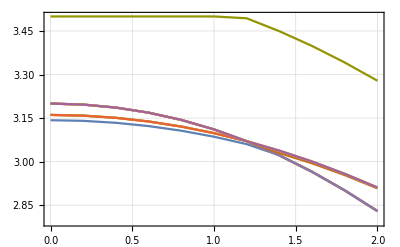

```mathematica
ListLinePlot[{vals1,vals2,vals3,vals4,vals5,vals6,vals7,vals8,vals9,vals10},Frame->True,GridLines->Automatic]
```

```mathematica
(** now we calculate the expection value of the square of spin <|S^2|>, S= s1+s2+s4+s5*)
```

```mathematica
spinpow=spinspin[a[1],a[1]]+spinspin[a[2],a[2]]+spinspin[a[4],a[4]]+spinspin[a[5],a[5]]+2spinspin[a[1],a[2]]+2spinspin[a[1],a[4]]+2spinspin[a[1],a[5]]+2spinspin[a[4],a[5]]+2spinspin[a[2],a[4]]+2spinspin[a[2],a[5]]//Simplify
```

1/4 (3 a_(1↓)^†·a_(1↓)^+3 a_(1⇑)^†·a_(1⇑)^+3 a_(2↓)^†·a_(2↓)^+3 a_(2⇑)^†·a_(2⇑)^+3 a_(4↓)^†·a_(4↓)^+3 a_(4⇑)^†·a_(4⇑)^+3 a_(5↓)^†·a_(5↓)^+3 a_(5⇑)^†·a_(5⇑)^+6 a_(1↓)^†·a_(1⇑)^†·a_(1↓)^·a_(1⇑)^-2 a_(1↓)^†·a_(2↓)^†·a_(1↓)^·a_(2↓)^+2 a_(1↓)^†·a_(2⇑)^†·a_(1↓)^·a_(2⇑)^-4 a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^-2 a_(1↓)^†·a_(4↓)^†·a_(1↓)^·a_(4↓)^+2 a_(1↓)^†·a_(4⇑)^†·a_(1↓)^·a_(4⇑)^-4 a_(1↓)^†·a_(4⇑)^†·a_(1⇑)^·a_(4↓)^-2 a_(1↓)^†·a_(5↓)^†·a_(1↓)^·a_(5↓)^+2 a_(1↓)^†·a_(5⇑)^†·a_(1↓)^·a_(5⇑)^-4 a_(1↓)^†·a_(5⇑)^†·a_(1⇑)^·a_(5↓)^-4 a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^+2 a_(1⇑)^†·a_(2↓)^†·a_(1⇑)^·a_(2↓)^-2 a_(1⇑)^†·a_(2⇑)^†·a_(1⇑)^·a_(2⇑)^-4 a_(1⇑)^†·a_(4↓)^†·a_(1↓)^·a_(4⇑)^+2 a_(1⇑)^†·a_(4↓)^†·a_(1⇑)^·a_(4↓)^-2 a_(1⇑)^†·a_(4⇑)^†·a_(1⇑)^·a_(4⇑)^-4 a_(1⇑)^†·a_(5↓)^†·a_(1↓)^·a_(5⇑)^+2 a_(1⇑)^†·a_(5↓)^†·a_(1⇑)^·a_(5↓)^-2 a_(1⇑)^†·a_(5⇑)^†·a_(1⇑)^·a_(5⇑)^+6 a_(2↓)^†·a_(2⇑)^†·a_(2↓)^·a_(2⇑)^-2 a_(2↓)^†·a_(4↓)^†·a_(2↓)^·a_(4↓)^+2 a_(2↓)^†·a_(4⇑)^†·a_(2↓)^·a_(4⇑)^-4 a_(2↓)^†·a_(4⇑)^†·a_(2⇑)^·a_(4↓)^-2 a_(2↓)^†·a_(5↓)^†·a_(2↓)^·a_(5↓)^+2 a_(2↓)^†·a_(5⇑)^†·a_(2↓)^·a_(5⇑)^-4 a_(2↓)^†·a_(5⇑)^†·a_(2⇑)^·a_(5↓)^-4 a_(2⇑)^†·a_(4↓)^†·a_(2↓)^·a_(4⇑)^+2 a_(2⇑)^†·a_(4↓)^†·a_(2⇑)^·a_(4↓)^-2 a_(2⇑)^†·a_(4⇑)^†·a_(2⇑)^·a_(4⇑)^-4 a_(2⇑)^†·a_(5↓)^†·a_(2↓)^·a_(5⇑)^+2 a_(2⇑)^†·a_(5↓)^†·a_(2⇑)^·a_(5↓)^-2 a_(2⇑)^†·a_(5⇑)^†·a_(2⇑)^·a_(5⇑)^+6 a_(4↓)^†·a_(4⇑)^†·a_(4↓)^·a_(4⇑)^-2 a_(4↓)^†·a_(5↓)^†·a_(4↓)^·a_(5↓)^+2 a_(4↓)^†·a_(5⇑)^†·a_(4↓)^·a_(5⇑)^-4 a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^-4 a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^+2 a_(4⇑)^†·a_(5↓)^†·a_(4⇑)^·a_(5↓)^-2 a_(4⇑)^†·a_(5⇑)^†·a_(4⇑)^·a_(5⇑)^+6 a_(5↓)^†·a_(5⇑)^†·a_(5↓)^·a_(5⇑)^)

```mathematica
Clear[avs2];
data1={};
Do[
Do[pos1=(Position[Eigensystem[mymat/.x->xx1][[1]],Sort[Eigensystem[mymat/.x->xx1][[1]]][[j]]]//Flatten)[[1]];
e1=Sort[Eigensystem[mymat/.x->xx1][[1]]][[j]];
wf1=Eigensystem[mymat/.x->xx1][[2,pos1]];
fullwf1=Sum[wf1[[i]]mybasis[[i]],{i,1,Dimensions[mybasis][[1]]}];
avs2=(matrixrepresentationop[spinpow,{fullwf1}]//Flatten)[[1]];
AppendTo[data1,{j,xx1,avs2,e1}];
Print[j];
Print[avs2],{xx1,0,2,0.1}],{j,1,10}]
```

1

0.0000168185

1

0.000352081

1

0.00135875

1

0.00303937

1

0.00539773

1

0.00843834

1

0.0121655

1

0.0165824

1

0.0216897

1

0.0274844

1

0.0339584

1

0.0410968

1

0.0488772

1

0.0572683

1

5.73559

1

5.69013

1

5.64173

1

5.5909

1

5.53825

1

5.48436

1

5.42982

2

1.99999

2

1.9998

2

1.99924

2

1.99831

2

1.99701

2

1.99534

2

1.9933

2

1.99091

2

1.98817

2

1.98508

2

1.98165

2

1.97788

2

5.81592

2

5.77763

2

5.73559

2

5.69013

2

5.64173

2

5.5909

2

5.53825

2

5.48436

2

5.42982

3

1.99999

3

1.9998

3

1.99924

3

1.99831

3

1.99701

3

1.99534

3

1.9933

3

1.99091

3

1.98817

3

1.98508

3

1.98165

3

1.97788

3

5.81592

3

5.77763

3

5.73559

3

5.69013

3

5.64173

3

5.5909

3

5.53825

3

5.48436

3

5.42982

4

1.99999

4

1.9998

4

1.99924

4

1.99831

4

1.99701

4

1.99534

4

1.9933

4

1.99091

4

1.98817

4

1.98508

4

1.98165

4

1.97788

4

5.81592

4

5.77763

4

5.73559

4

5.69013

4

5.64173

4

5.5909

4

5.53825

4

5.48436

4

5.42982

5

6.

5

5.99908

5

5.99627

5

5.99146

5

5.98446

5

5.97502

5

5.96283

5

5.94758

5

5.92896

5

5.90666

5

5.88047

5

5.85023

5

5.81592

5

5.77763

5

5.73559

5

5.69013

5

5.64173

5

5.5909

5

5.53825

5

5.48436

5

5.42982

6

6.

6

5.99908

6

5.99627

6

5.99146

6

5.98446

6

5.97502

6

5.96283

6

5.94758

6

5.92896

6

5.90666

6

5.88047

6

5.85023

6

5.81592

6

5.77763

6

0.0662294

6

0.0757101

6

0.0856509

6

0.0959838

6

0.106634

6

0.117521

6

0.128563

7

6.

7

5.99908

7

5.99627

7

5.99146

7

5.98446

7

5.97502

7

5.96283

7

5.94758

7

5.92896

7

5.90666

7

5.88047

7

5.85023

7

1.97379

7

1.96938

7

1.96465

7

1.95963

7

1.9543

7

1.94868

7

1.94279

7

1.93661

7

1.93017

8

6.

8

5.99908

8

5.99627

8

5.99146

8

5.98446

8

5.97502

8

5.96283

8

5.94758

8

5.92896

8

5.90666

8

5.88047

8

5.85023

8

1.97379

8

1.96938

8

1.96465

8

1.95963

8

1.9543

8

1.94868

8

1.94279

8

1.93661

8

1.93017

9

6.

9

5.99908

9

5.99627

9

5.99146

9

5.98446

9

5.97502

9

5.96283

9

5.94758

9

5.92896

9

5.90666

9

5.88047

9

5.85023

9

1.97379

9

1.96938

9

1.96465

9

1.95963

9

1.9543

9

1.94868

9

1.94279

9

1.93661

9

1.93017

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

0.734939

10

0.732901

10

0.730851

10

0.728811

10

0.726798

10

0.72483

10

0.72292

10

0.721083

10

0.719327

```mathematica
data1//MatrixForm
```

(1 | 0. | 0.0000168185 | 3.14274
1 | 0.1 | 0.000352081 | 3.14218
1 | 0.2 | 0.00135875 | 3.1405
1 | 0.3 | 0.00303937 | 3.1377
1 | 0.4 | 0.00539773 | 3.13376
1 | 0.5 | 0.00843834 | 3.1287
1 | 0.6 | 0.0121655 | 3.12248
1 | 0.7 | 0.0165824 | 3.1151
1 | 0.8 | 0.0216897 | 3.10655
1 | 0.9 | 0.0274844 | 3.09682
1 | 1. | 0.0339584 | 3.08588
1 | 1.1 | 0.0410968 | 3.07372
1 | 1.2 | 0.0488772 | 3.06033
1 | 1.3 | 0.0572683 | 3.0457
1 | 1.4 | 5.73559 | 3.02172
1 | 1.5 | 5.69013 | 2.99438
1 | 1.6 | 5.64173 | 2.96511
1 | 1.7 | 5.5909 | 2.93394
1 | 1.8 | 5.53825 | 2.90094
1 | 1.9 | 5.48436 | 2.86619
1 | 2. | 5.42982 | 2.82978
2 | 0. | 1.99999 | 3.161
2 | 0.1 | 1.9998 | 3.16037
2 | 0.2 | 1.99924 | 3.15848
2 | 0.3 | 1.99831 | 3.15534
2 | 0.4 | 1.99701 | 3.15094
2 | 0.5 | 1.99534 | 3.14528
2 | 0.6 | 1.9933 | 3.13836
2 | 0.7 | 1.99091 | 3.13019
2 | 0.8 | 1.98817 | 3.12076
2 | 0.9 | 1.98508 | 3.11007
2 | 1. | 1.98165 | 3.09814
2 | 1.1 | 1.97788 | 3.08495
2 | 1.2 | 5.81592 | 3.07041
2 | 1.3 | 5.77763 | 3.04707
2 | 1.4 | 5.73559 | 3.02172
2 | 1.5 | 5.69013 | 2.99438
2 | 1.6 | 5.64173 | 2.96511
2 | 1.7 | 5.5909 | 2.93394
2 | 1.8 | 5.53825 | 2.90094
2 | 1.9 | 5.48436 | 2.86619
2 | 2. | 5.42982 | 2.82978
3 | 0. | 1.99999 | 3.161
3 | 0.1 | 1.9998 | 3.16037
3 | 0.2 | 1.99924 | 3.15848
3 | 0.3 | 1.99831 | 3.15534
3 | 0.4 | 1.99701 | 3.15094
3 | 0.5 | 1.99534 | 3.14528
3 | 0.6 | 1.9933 | 3.13836
3 | 0.7 | 1.99091 | 3.13019
3 | 0.8 | 1.98817 | 3.12076
3 | 0.9 | 1.98508 | 3.11007
3 | 1. | 1.98165 | 3.09814
3 | 1.1 | 1.97788 | 3.08495
3 | 1.2 | 5.81592 | 3.07041
3 | 1.3 | 5.77763 | 3.04707
3 | 1.4 | 5.73559 | 3.02172
3 | 1.5 | 5.69013 | 2.99438
3 | 1.6 | 5.64173 | 2.96511
3 | 1.7 | 5.5909 | 2.93394
3 | 1.8 | 5.53825 | 2.90094
3 | 1.9 | 5.48436 | 2.86619
3 | 2. | 5.42982 | 2.82978
4 | 0. | 1.99999 | 3.161
4 | 0.1 | 1.9998 | 3.16037
4 | 0.2 | 1.99924 | 3.15848
4 | 0.3 | 1.99831 | 3.15534
4 | 0.4 | 1.99701 | 3.15094
4 | 0.5 | 1.99534 | 3.14528
4 | 0.6 | 1.9933 | 3.13836
4 | 0.7 | 1.99091 | 3.13019
4 | 0.8 | 1.98817 | 3.12076
4 | 0.9 | 1.98508 | 3.11007
4 | 1. | 1.98165 | 3.09814
4 | 1.1 | 1.97788 | 3.08495
4 | 1.2 | 5.81592 | 3.07041
4 | 1.3 | 5.77763 | 3.04707
4 | 1.4 | 5.73559 | 3.02172
4 | 1.5 | 5.69013 | 2.99438
4 | 1.6 | 5.64173 | 2.96511
4 | 1.7 | 5.5909 | 2.93394
4 | 1.8 | 5.53825 | 2.90094
4 | 1.9 | 5.48436 | 2.86619
4 | 2. | 5.42982 | 2.82978
5 | 0. | 6. | 3.2
5 | 0.1 | 5.99908 | 3.19914
5 | 0.2 | 5.99627 | 3.19657
5 | 0.3 | 5.99146 | 3.19225
5 | 0.4 | 5.98446 | 3.18619
5 | 0.5 | 5.97502 | 3.17834
5 | 0.6 | 5.96283 | 3.16867
5 | 0.7 | 5.94758 | 3.15715
5 | 0.8 | 5.92896 | 3.14373
5 | 0.9 | 5.90666 | 3.12837
5 | 1. | 5.88047 | 3.11105
5 | 1.1 | 5.85023 | 3.09174
5 | 1.2 | 5.81592 | 3.07041
5 | 1.3 | 5.77763 | 3.04707
5 | 1.4 | 5.73559 | 3.02172
5 | 1.5 | 5.69013 | 2.99438
5 | 1.6 | 5.64173 | 2.96511
5 | 1.7 | 5.5909 | 2.93394
5 | 1.8 | 5.53825 | 2.90094
5 | 1.9 | 5.48436 | 2.86619
5 | 2. | 5.42982 | 2.82978
6 | 0. | 6. | 3.2
6 | 0.1 | 5.99908 | 3.19914
6 | 0.2 | 5.99627 | 3.19657
6 | 0.3 | 5.99146 | 3.19225
6 | 0.4 | 5.98446 | 3.18619
6 | 0.5 | 5.97502 | 3.17834
6 | 0.6 | 5.96283 | 3.16867
6 | 0.7 | 5.94758 | 3.15715
6 | 0.8 | 5.92896 | 3.14373
6 | 0.9 | 5.90666 | 3.12837
6 | 1. | 5.88047 | 3.11105
6 | 1.1 | 5.85023 | 3.09174
6 | 1.2 | 5.81592 | 3.07041
6 | 1.3 | 5.77763 | 3.04707
6 | 1.4 | 0.0662294 | 3.02981
6 | 1.5 | 0.0757101 | 3.01267
6 | 1.6 | 0.0856509 | 2.99425
6 | 1.7 | 0.0959838 | 2.97457
6 | 1.8 | 0.106634 | 2.95361
6 | 1.9 | 0.117521 | 2.9314
6 | 2. | 0.128563 | 2.90794
7 | 0. | 6. | 3.2
7 | 0.1 | 5.99908 | 3.19914
7 | 0.2 | 5.99627 | 3.19657
7 | 0.3 | 5.99146 | 3.19225
7 | 0.4 | 5.98446 | 3.18619
7 | 0.5 | 5.97502 | 3.17834
7 | 0.6 | 5.96283 | 3.16867
7 | 0.7 | 5.94758 | 3.15715
7 | 0.8 | 5.92896 | 3.14373
7 | 0.9 | 5.90666 | 3.12837
7 | 1. | 5.88047 | 3.11105
7 | 1.1 | 5.85023 | 3.09174
7 | 1.2 | 1.97379 | 3.07051
7 | 1.3 | 1.96938 | 3.05483
7 | 1.4 | 1.96465 | 3.03792
7 | 1.5 | 1.95963 | 3.01978
7 | 1.6 | 1.9543 | 3.00041
7 | 1.7 | 1.94868 | 2.97984
7 | 1.8 | 1.94279 | 2.95806
7 | 1.9 | 1.93661 | 2.93511
7 | 2. | 1.93017 | 2.91098
8 | 0. | 6. | 3.2
8 | 0.1 | 5.99908 | 3.19914
8 | 0.2 | 5.99627 | 3.19657
8 | 0.3 | 5.99146 | 3.19225
8 | 0.4 | 5.98446 | 3.18619
8 | 0.5 | 5.97502 | 3.17834
8 | 0.6 | 5.96283 | 3.16867
8 | 0.7 | 5.94758 | 3.15715
8 | 0.8 | 5.92896 | 3.14373
8 | 0.9 | 5.90666 | 3.12837
8 | 1. | 5.88047 | 3.11105
8 | 1.1 | 5.85023 | 3.09174
8 | 1.2 | 1.97379 | 3.07051
8 | 1.3 | 1.96938 | 3.05483
8 | 1.4 | 1.96465 | 3.03792
8 | 1.5 | 1.95963 | 3.01978
8 | 1.6 | 1.9543 | 3.00041
8 | 1.7 | 1.94868 | 2.97984
8 | 1.8 | 1.94279 | 2.95806
8 | 1.9 | 1.93661 | 2.93511
8 | 2. | 1.93017 | 2.91098
9 | 0. | 6. | 3.2
9 | 0.1 | 5.99908 | 3.19914
9 | 0.2 | 5.99627 | 3.19657
9 | 0.3 | 5.99146 | 3.19225
9 | 0.4 | 5.98446 | 3.18619
9 | 0.5 | 5.97502 | 3.17834
9 | 0.6 | 5.96283 | 3.16867
9 | 0.7 | 5.94758 | 3.15715
9 | 0.8 | 5.92896 | 3.14373
9 | 0.9 | 5.90666 | 3.12837
9 | 1. | 5.88047 | 3.11105
9 | 1.1 | 5.85023 | 3.09174
9 | 1.2 | 1.97379 | 3.07051
9 | 1.3 | 1.96938 | 3.05483
9 | 1.4 | 1.96465 | 3.03792
9 | 1.5 | 1.95963 | 3.01978
9 | 1.6 | 1.9543 | 3.00041
9 | 1.7 | 1.94868 | 2.97984
9 | 1.8 | 1.94279 | 2.95806
9 | 1.9 | 1.93661 | 2.93511
9 | 2. | 1.93017 | 2.91098
10 | 0. | 3.75 | 3.5
10 | 0.1 | 3.75 | 3.5
10 | 0.2 | 3.75 | 3.5
10 | 0.3 | 3.75 | 3.5
10 | 0.4 | 3.75 | 3.5
10 | 0.5 | 3.75 | 3.5
10 | 0.6 | 3.75 | 3.5
10 | 0.7 | 3.75 | 3.5
10 | 0.8 | 3.75 | 3.5
10 | 0.9 | 3.75 | 3.5
10 | 1. | 3.75 | 3.5
10 | 1.1 | 3.75 | 3.5
10 | 1.2 | 0.734939 | 3.49373
10 | 1.3 | 0.732901 | 3.47225
10 | 1.4 | 0.730851 | 3.44917
10 | 1.5 | 0.728811 | 3.42452
10 | 1.6 | 0.726798 | 3.39833
10 | 1.7 | 0.72483 | 3.37062
10 | 1.8 | 0.72292 | 3.34141
10 | 1.9 | 0.721083 | 3.31074
10 | 2. | 0.719327 | 3.27861)

```mathematica
(****now we calculate J1 and J2 as well as β = -J2/J1, J1= (1/2)(E2-E1), J2 = E0/3+E2/6-E1/2****)
```

```mathematica
Dimensions[data1]
```

{210,4}

```mathematica
tmp01=data1[[1;;14,1;;4]];
tmp02=data1[[120;;126,1;;4]];
tmp04=Flatten[{tmp01,tmp02},1];
e0data=Table[{tmp04[[i,2]],tmp04[[i,4]],tmp04[[i,3]]},{i,Dimensions[tmp04][[1]]}];
```

```mathematica
tmp01=data1[[22;;33,1;;4]];
tmp02=data1[[181;;189,1;;4]];
tmp03=Flatten[{tmp01,tmp02},1];
e1data=Table[{tmp03[[i,2]],tmp03[[i,4]],tmp03[[i,3]]},{i,Dimensions[tmp03][[1]]}];
```

```mathematica
tmp01=data1[[85;;105,1;;4]];
tmp03=Flatten[{tmp01},1];
e2data=Table[{tmp03[[i,2]],tmp03[[i,4]],tmp03[[i,3]]},{i,Dimensions[tmp03][[1]]}];
```

```mathematica
tmp03=data1[[190;;210,1;;4]];

e4data=Table[{tmp03[[i,2]],tmp03[[i,4]],tmp03[[i,3]]},{i,Dimensions[tmp03][[1]]}];
```

```mathematica
e0data//MatrixForm
e1data//MatrixForm
e2data//MatrixForm
```

(0. | 3.14274 | 0.0000168185
0.1 | 3.14218 | 0.000352081
0.2 | 3.1405 | 0.00135875
0.3 | 3.1377 | 0.00303937
0.4 | 3.13376 | 0.00539773
0.5 | 3.1287 | 0.00843834
0.6 | 3.12248 | 0.0121655
0.7 | 3.1151 | 0.0165824
0.8 | 3.10655 | 0.0216897
0.9 | 3.09682 | 0.0274844
1. | 3.08588 | 0.0339584
1.1 | 3.07372 | 0.0410968
1.2 | 3.06033 | 0.0488772
1.3 | 3.0457 | 0.0572683
1.4 | 3.02981 | 0.0662294
1.5 | 3.01267 | 0.0757101
1.6 | 2.99425 | 0.0856509
1.7 | 2.97457 | 0.0959838
1.8 | 2.95361 | 0.106634
1.9 | 2.9314 | 0.117521
2. | 2.90794 | 0.128563)

(0. | 3.161 | 1.99999
0.1 | 3.16037 | 1.9998
0.2 | 3.15848 | 1.99924
0.3 | 3.15534 | 1.99831
0.4 | 3.15094 | 1.99701
0.5 | 3.14528 | 1.99534
0.6 | 3.13836 | 1.9933
0.7 | 3.13019 | 1.99091
0.8 | 3.12076 | 1.98817
0.9 | 3.11007 | 1.98508
1. | 3.09814 | 1.98165
1.1 | 3.08495 | 1.97788
1.2 | 3.07051 | 1.97379
1.3 | 3.05483 | 1.96938
1.4 | 3.03792 | 1.96465
1.5 | 3.01978 | 1.95963
1.6 | 3.00041 | 1.9543
1.7 | 2.97984 | 1.94868
1.8 | 2.95806 | 1.94279
1.9 | 2.93511 | 1.93661
2. | 2.91098 | 1.93017)

(0. | 3.2 | 6.
0.1 | 3.19914 | 5.99908
0.2 | 3.19657 | 5.99627
0.3 | 3.19225 | 5.99146
0.4 | 3.18619 | 5.98446
0.5 | 3.17834 | 5.97502
0.6 | 3.16867 | 5.96283
0.7 | 3.15715 | 5.94758
0.8 | 3.14373 | 5.92896
0.9 | 3.12837 | 5.90666
1. | 3.11105 | 5.88047
1.1 | 3.09174 | 5.85023
1.2 | 3.07041 | 5.81592
1.3 | 3.04707 | 5.77763
1.4 | 3.02172 | 5.73559
1.5 | 2.99438 | 5.69013
1.6 | 2.96511 | 5.64173
1.7 | 2.93394 | 5.5909
1.8 | 2.90094 | 5.53825
1.9 | 2.86619 | 5.48436
2. | 2.82978 | 5.42982)

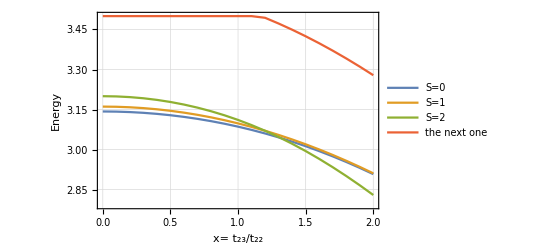

```mathematica
ListLinePlot[{e0data[[1;;21,1;;2]],e1data[[1;;21,1;;2]],e2data[[1;;21,1;;2]],e4data[[1;;21,1;;2]]},PlotLegends->{"S=0","S=1","S=2","the next one"},Frame->True,GridLines->Automatic,AxesLabel->{"x= t_23/t_22","Energy"}]
```

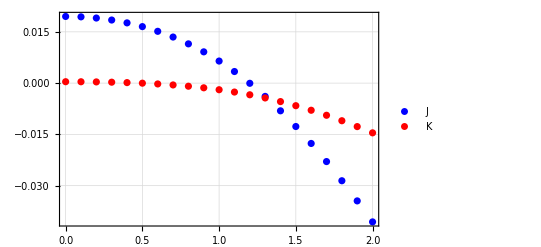

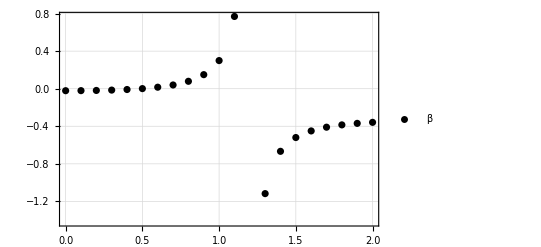

```mathematica
jj1=Table[{e2data[[i,1]],(e2data[[i,2]]-e1data[[i,2]])/2},{i,1,Dimensions[e1data][[1]]}];
jj2=Table[{e2data[[i,1]],e0data[[i,2]]/3.0+e2data[[i,2]]/6.0-e1data[[i,2]]/2.0},{i,1,Dimensions[e1data][[1]]}];
beta=Table[{e2data[[i,1]],-jj2[[i,2]]/jj1[[i,2]]},{i,1,Dimensions[jj1][[1]]}];
ListPlot[{jj1,jj2},PlotRange->Automatic,Frame->True,GridLines->Automatic,PlotLegends->Placed[{"J","K"},{Left,Center}],PlotStyle->{Blue,Red}]
ListPlot[beta,PlotRange->Automatic,Frame->True,GridLines->Automatic,PlotLegends->Placed[{"β"},{Left,Center}],PlotStyle->Black]
```